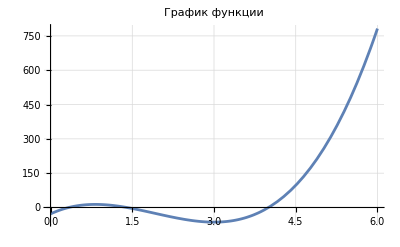

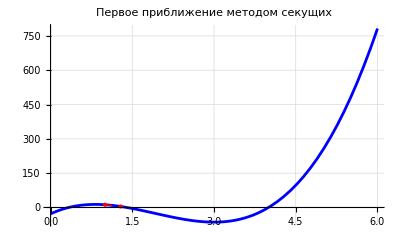
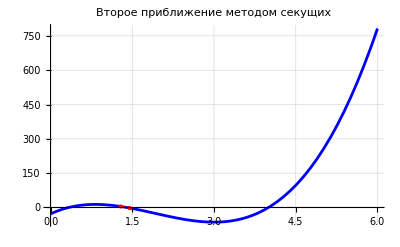

Корень методом секущих: 1.4, Количество итераций: 4

```mathematica
(*###################################################################################*)
(*1*)
(*Определяем функцию*)f[x_]:=15 x^3-86 x^2+111 x-28

(*Построим график функции*)
Plot[f[x],{x,0,6},GridLines->Automatic,AxesOrigin->{0,0},PlotLabel->"График функции",PlotRange->All]

(*Метод секущих с иллюстрацией первых двух приближений*)
SecantMethodWithPlot[f_,x0_,x1_,eps_]:=Module[{x2,xold=x1,xnew=x0,count=0,plots},plots={};(*Список для хранения промежуточных графиков*)(*Первое приближение*)x2=xnew-(f[xnew]*(xnew-xold))/(f[xnew]-f[xold]);
AppendTo[plots,Show[Plot[f[x],{x,0,6},PlotRange->All,PlotStyle->Blue,GridLines->Automatic,PlotLabel->"Первое приближение методом секущих"],Graphics[{Red,PointSize[Large],Point[{xnew,f[xnew]}],Point[{x2,f[x2]}],Dashed,Line[{{xnew,f[xnew]},{x2,f[x2]}}]}]]];
xold=xnew;xnew=x2;
(*Второе приближение*)x2=xnew-(f[xnew]*(xnew-xold))/(f[xnew]-f[xold]);
AppendTo[plots,Show[Plot[f[x],{x,0,6},PlotRange->All,PlotStyle->Blue,GridLines->Automatic,PlotLabel->"Второе приближение методом секущих"],Graphics[{Red,PointSize[Large],Point[{xnew,f[xnew]}],Point[{x2,f[x2]}],Dashed,Line[{{xnew,f[xnew]},{x2,f[x2]}}]}]]];
(*Итерации метода секущих до заданной точности*)While[Abs[f[xnew]]>eps,x2=xnew-(f[xnew]*(xnew-xold))/(f[xnew]-f[xold]);
xold=xnew;xnew=x2;
count++;];
(*Возвращаем корень и промежуточные графики*){N[xnew],count,plots}]

(*Найдем корень и выведем промежуточные графики*)
{root,iterations,secantPlots}=SecantMethodWithPlot[f,1,2,10^-3];
secantPlots (*Отобразим промежуточные графики*)
Print["Корень методом секущих: ",root,", Количество итераций: ",iterations]
```

```mathematica
(*###################################################################################*)
(*2*)
```

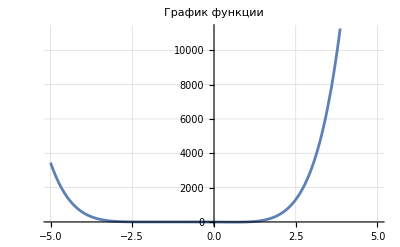

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{x→-2},{x→-2},{x→-1},{x→-1},{x→-1},{x→1}}

{{x→-2.},{x→-2.},{x→-1.},{x→-1.},{x→-1.},{x→1.}}

x==-2||x==-2||x==-1||x==-1||x==-1||x==1

{x→-0.999993}

(-1+x) (1+x)^3 (2+x)^2

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
f[x_]:=x^6+6x^5+12x^4+6x^3-9x^2-12x-4

Plot[f[x],{x,-5,5},GridLines->Automatic,PlotLabel->"График функции"]

(*Метод Solve-аналитическое решение*)
analyticalRoots=Solve[f[x]==0,x];

(*Метод NSolve-численное решение*)
numericalRoots=NSolve[f[x]==0,x];

(*Метод Roots-нахождение корней*)
rootsEquationForm=Roots[f[x]==0,x];

(*Метод FindRoot-нахождение корня при начальном приближении*)
findRootExample=FindRoot[f[x]==0,{x,0}];

(*Шаг 3:Разложение многочлена на множители*)
factorization=Factor[f[x]];
Print[analyticalRoots]
Print[numericalRoots]
Print[rootsEquationForm]
Print[findRootExample]
Print[factorization]
```

```mathematica
(*###################################################################################*)
(*3*)
```

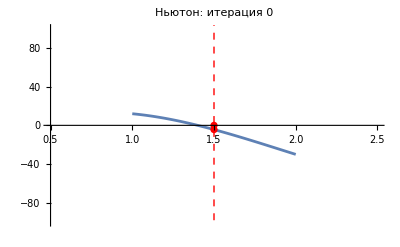

Метод Ньютона: найден корень x = 3/2+35/(8 ∂_(3/2) (-35/8)) за 1 итераций.

Метод секущих:

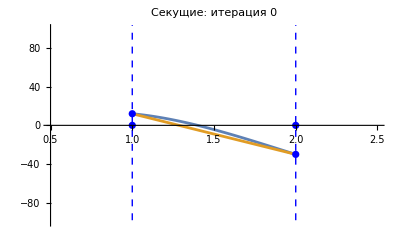

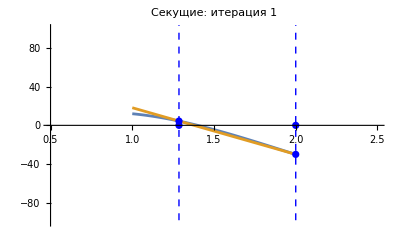

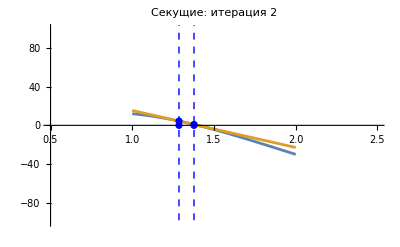

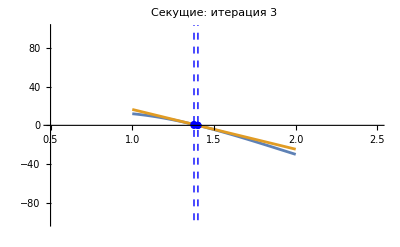

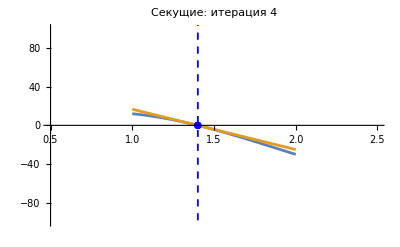

Метод секущих: найден корень x = 14168533021361925221653918898779838978589128300821564330016966026/10120380871295085143675132966144240944485674993451556263723163703 за 5 итераций.

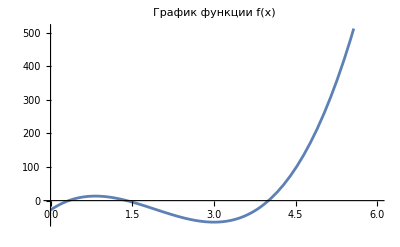

Метод Ньютона:

D::ivar: 3/2 is not a valid variable.

D::ivar: 1.5 is not a valid variable.

D::ivar: 3/2 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

-Graphics-

Метод Ньютона: найден корень x = 3/2+35/(8 ∂_(3/2) (-35/8)) за 1 итераций.

Метод секущих:

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Метод секущих: найден корень x = 14168533021361925221653918898779838978589128300821564330016966026/10120380871295085143675132966144240944485674993451556263723163703 за 5 итераций.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit::reclim will be suppressed during this calculation.

```mathematica
(*Задаём функцию f(x)=15x^3-86x^2+111x-28*)f[x_]:=15*x^3-86*x^2+111*x-28;

(*Выводим график функции*)
Plot[f[x],{x,0,6},AxesOrigin->{0,0},PlotLabel->"График функции f(x)"]

(*Начальные значения для метода Ньютона и секущих*)
a=1;
b=2;
eps=0.001;  (*точность*)
maxIter=100;  (*максимальное количество итераций*)

(*Метод Ньютона*)

(*Производная функции для метода Ньютона*)
fPrime[x_]:=D[f[x],x];

(*Начальное приближение для метода Ньютона*)
xnNewton=(a+b)/2;
nNewton=0;

Print["Метод Ньютона:"];

While[Abs[f[xnNewton]]>eps&&nNewton<maxIter,(*Вывод графика на каждой итерации*)Print[Plot[{f[x],f[xnNewton]+fPrime[xnNewton] (x-xnNewton)},{x,a,b},Epilog->{Red,Dashed,InfiniteLine[{xnNewton,0},{0,1}],PointSize[0.013],Point[{{xnNewton,0},{xnNewton,f[xnNewton]}}]},PlotLabel->"Ньютон: итерация "<>ToString[nNewton],PlotRange->{{a-0.5,b+0.5},{-100,100}}]];
(*Следующее приближение по методу Ньютона*)xnNewton=xnNewton-f[xnNewton]/fPrime[xnNewton];
nNewton++;]

If[nNewton>=maxIter,Print["Метод Ньютона не сошелся за ",maxIter," итераций."],Print["Метод Ньютона: найден корень x = ",xnNewton," за ",nNewton," итераций."]];

(*Метод секущих*)

Print["Метод секущих:"];

(*Начальные значения для метода секущих*)
xnSecPrev=a;
xnSec=b;
nSec=0;

While[Abs[xnSec-xnSecPrev]>eps&&nSec<maxIter,(*Вывод графика на каждой итерации*)Print[Plot[{f[x],f[xnSec]+((f[xnSec]-f[xnSecPrev])/(xnSec-xnSecPrev))*(x-xnSec)},{x,a,b},Epilog->{Blue,Dashed,InfiniteLine[{xnSec,0},{0,1}],InfiniteLine[{xnSecPrev,0},{0,1}],PointSize[0.013],Point[{{xnSec,0},{xnSec,f[xnSec]},{xnSecPrev,0},{xnSecPrev,f[xnSecPrev]}}]},PlotLabel->"Секущие: итерация "<>ToString[nSec],PlotRange->{{a-0.5,b+0.5},{-100,100}}]];
(*Следующее приближение по методу секущих*)xnSecNext=xnSec-f[xnSec]*(xnSec-xnSecPrev)/(f[xnSec]-f[xnSecPrev]);
xnSecPrev=xnSec;
xnSec=xnSecNext;
nSec++;]

If[nSec>=maxIter,Print["Метод секущих не сошелся за ",maxIter," итераций."],Print["Метод секущих: найден корень x = ",xnSec," за ",nSec," итераций."]];
```

```mathematica
(*###################################################################################*)
(*4*)
```

D::ivar: 0.5` is not a valid variable.

```mathematica
phi[x_]:=Log[4 x+2]/Log[3]

(*Метод простых итераций*)
simpleIteration[x0_,tol_,maxIter_]:=Module[{x=x0,xNext,i=0},While[i<maxIter&&Abs[phi[x]-x]>tol,xNext=phi[x];
If[Abs[xNext-x]<tol,Break[]];
x=xNext;
i++];
{N[x],i}]

(*Применяем метод простых итераций с начальным приближением x0=0.5*)
rootSimpleIter=simpleIteration[0.5,10^-3,100]
```

{2.1477,8}

```mathematica
(*###################################################################################*)
(*5*)
```

```mathematica
eqn=3^x==4x+2;

(*Решаем уравнение с помощью Solve*)
solveRoot=Solve[eqn,x]

(*Решаем уравнение с помощью NSolve для численного решения*)
nsolveRoot=NSolve[eqn,x]

(*Решаем уравнение с помощью FindRoot с начальным приближением*)
findRoot=FindRoot[eqn,{x,0.5}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(-Log[3]-2 ProductLog[-Log[3]/(4 √3)])/(2 Log[3])},{x→(-Log[3]-2 ProductLog[-1,-Log[3]/(4 √3)])/(2 Log[3])}}

{{x→-0.325081},{x→3.1091-6.6992 ⅈ},{x→3.1091+6.6992 ⅈ},{x→3.61294+12.5806 ⅈ},{x→3.9372+18.3717 ⅈ},{x→4.17643+24.1324 ⅈ},{x→4.36599+29.8789 ⅈ},{x→4.52296+35.6175 ⅈ},{x→4.65689+41.3513 ⅈ},{x→4.77367+47.0819 ⅈ},{x→4.8772+52.8103 ⅈ},{x→4.97018+58.537 ⅈ},{x→6.14241-213.012 ⅈ},{x→2.14839},{x→5.05455+64.2625 ⅈ},{x→5.13178+69.9871 ⅈ}}

{x→-0.325081}

```mathematica
(*###################################################################################*)
(*6*)
```

{{x→,y→},{x→,y→},{x→,y→},{x→,y→}}

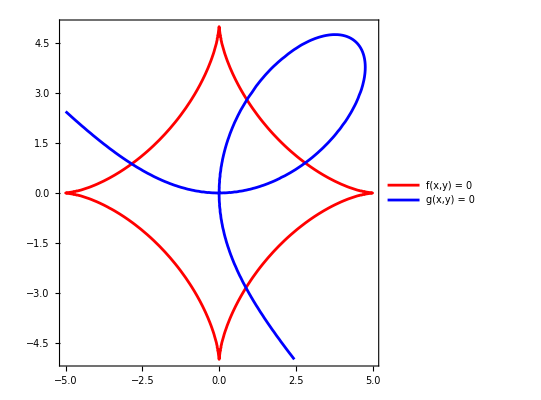

```mathematica
eq1=CubeRoot[x^2]+CubeRoot[y^2]==CubeRoot[25];
eq2=x^3+y^3-9*x*y==0;

(*Решаем систему уравнений*)
solutions=Solve[{eq1,eq2},{x,y}];

(*Выводим найденные решения*)
solutions

(*Графическое отображение кривых*)
ContourPlot[{CubeRoot[x^2]+CubeRoot[y^2]==CubeRoot[25],x^3+y^3-9*x*y==0},{x,-5,5},{y,-5,5},PlotLegends->{"f(x,y) = 0","g(x,y) = 0"},ContourStyle->{Red,Blue}]
```